```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}, ColorFunction->GrayLevel]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Plot3D[If[Or[EuclideanDistance[{0, 0}, {x, y}] > 0.5, EuclideanDistance[{0, 0}, {x, y}] < 0.2],Im[ArcSin[(x+I y)^4]], None],{x,-2,2},{y,-2,2},Mesh->None,ColorFunction->GrayLevel, PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
data=Flatten[Table[{r Cos[t],r Sin[t],Sinc[r]},{r,0,10,0.5},{t,0,2Pi,0.1}],1];
```

```mathematica
ListPointPlot3D[data]
```

-Graphics3D-

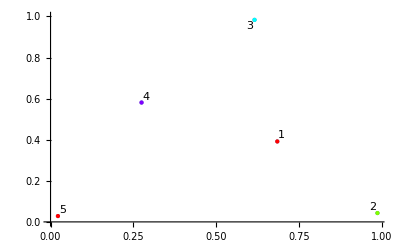

```mathematica
ListPlot[MapThread[Labeled[#1, #2] & , {Table[Style[{RandomReal[],RandomReal[]},Hue[t/(2Pi)]],{t,0,2Pi,Pi/2}], Range[5]}],PlotStyle->PointSize[Large],LabelStyle->Large, PlotRange->{0, 1}]
```